# WolframInstitute/TuringMachine

Tools for exploring and analyzing Turing machines

## Paclet Manifest

## Web Content

### Headline Image

```mathematica
With[{
   evolution = Function[input,
      OneSidedTuringMachinePlot[{600720, 3, 2}, input, 16, "LabelOutput" -> False]]},
 ImageResize[
  Rasterize[
   Framed[
    Column[{
       Style["TuringMachine", 30, Bold, GrayLevel[0.15], FontFamily -> "Source Sans Pro"],
       Style["Exploring and analyzing Turing machines", 13, GrayLevel[0.45], FontFamily -> "Source Sans Pro"],
       Spacer[14],
       Row[{evolution[10], evolution[106]}, Spacer[24]]},
      Alignment -> Center, Spacings -> 1.0],
    Background -> GrayLevel[0.98], FrameMargins -> 30, FrameStyle -> GrayLevel[0.9], RoundingRadius -> 16],
   ImageResolution -> 144, Background -> None],
  {Automatic, 520}]]
```

-Graphics-

### Basic Description

The paclet identifies a Turing machine by its enumeration number and its {s, k} state/color counts. OneSidedTuringMachineFunction runs a one-sided machine on an integer input and returns its halting value, step count, or tape width; OneSidedTuringMachinePlot draws the space-time evolution; and OneSidedTuringMachineFind searches for machines reproducing given outputs. The MultiwayTuringMachineFunction family explores nondeterministic (multiway) machines, while TuringMachineRuleCount and the TuringMachineOutput primitives tabulate behavior across whole rule spaces. TuringMachineToTagSystem, TagSystemToCyclicTagSystem, CyclicTagSystemToSystem5, System5ToSystem4, System4ToSystem3 and System3ToWolfram23 carry a Turing machine along the chain of Smith's universality proof to Wolfram's 2,3 machine.

### Details

A Turing machine is specified by its Wolfram enumeration number together with its state and color counts, written {number, s, k} — for example {600720, 3, 2} is rule 600720 with 3 states and 2 colors.

The one-sided functions read a non-negative integer input off the tape, run the machine, and report the halting value, the number of steps taken, or the maximum tape width reached.

A machine that does not halt within the given step bound reports Infinity / Undefined for the parts it could not resolve.

The multiway functions explore nondeterministic machines, where a {state, color} pair may carry several transitions, and return all reachable configurations.

A Rust backend (loaded from the paclet's Binaries) accelerates the bulk enumeration and search functions over whole rule spaces.

The chain of Alex Smith's proof that Wolfram's 2,3 Turing machine is universal has one function per arrow, from a binary Turing machine through a 2-tag system, a cyclic tag system and Smith's Systems 5, 4 and 3 to the 2,3 machine, with a decoder for each way back and an evolution function for each system. Each follows the Lean formalization of the proof in the paclet's repository.

### Primary Context

WolframInstitute`TuringMachine`

### Main Guide Page

## Examples

### Initialization for Examples

```mathematica
PacletDirectoryLoad[NotebookDirectory[]];
```

```mathematica
Needs["WolframInstitute`TuringMachine`"];
```

### Basic Examples

Run the one-sided Turing machine defined by the s=3, k=2 rule 600720 on input 1 for at most 32 steps:

```mathematica
OneSidedTuringMachineFunction[{600720, 3, 2}, 1, 32]
```

7

Return the number of steps the machine took to terminate:

```mathematica
OneSidedTuringMachineFunction[{600720, 3, 2}, 1, 32, "Steps"]
```

5

Return the maximum width the head spanned on the tape:

```mathematica
OneSidedTuringMachineFunction[{600720, 3, 2}, 1, 32, "Width"]
```

3

Return the steps, value, and width together:

```mathematica
OneSidedTuringMachineFunction[{600720, 3, 2}, 1, 32, All]
```

{5,7,3}

Plot the space-time evolution of the machine on input 1:

```mathematica
OneSidedTuringMachinePlot[{600720, 3, 2}, 1, {5, 3}]
```

-Graphics-

### Scope

Evaluate a whole family of machines at once — every s=1, k=2 one-sided machine on inputs 1 through 8, each for up to 32 steps:

```mathematica
OneSidedTuringMachineFunction[{All, 1, 2}, {1, 8}, 32]
```

{{Undefined,Undefined,Undefined,Undefined,Undefined,Undefined,Undefined,Undefined},{0,2,0,4,4,6,0,8},{Undefined,Undefined,Undefined,Undefined,Undefined,Undefined,Undefined,Undefined},{3,3,7,5,7,7,15,9},{0,Undefined,2,Undefined,4,Undefined,6,Undefined},{0,2,2,4,4,6,6,8},{0,0,2,0,4,4,6,0},{0,3,2,5,4,7,6,9},{Undefined,Undefined,Undefined,Undefined,Undefined,Undefined,Undefined,Undefined},{Undefined,2,Undefined,4,Undefined,6,Undefined,8},{Undefined,Undefined,Undefined,Undefined,Undefined,Undefined,Undefined,Undefined},{Undefined,3,Undefined,5,Undefined,7,Undefined,9},{1,Undefined,3,Undefined,5,Undefined,7,Undefined},{1,2,3,4,5,6,7,8},{1,3,3,7,5,7,7,15},{1,3,3,5,5,7,7,9}}

Count how many distinct Turing machine rules exist for a given number of states and colors:

```mathematica
TuringMachineRuleCount[3, 2]
```

2985984

### Options

Split a long evolution into several columns with the "Columns" option:

```mathematica
OneSidedTuringMachinePlot[{600720, 3, 2}, 106, 16, "Columns" -> 3]
```

-Graphics-

Suppress the output label to show the bare space-time pattern:

```mathematica
OneSidedTuringMachinePlot[{600720, 3, 2}, 106, 16, "LabelOutput" -> False]
```

-Graphics-

### Applications

Search the 2-state, 2-color rule space for the machines that reproduce a target behavior, given as {input, steps, value} triples:

```mathematica
Length[OneSidedTuringMachineFind[{{1, 3, 3}, {2, 1, 3}}, {2, 2}]]
```

132

Compare how a single machine transforms several different inputs:

```mathematica
GraphicsRow[OneSidedTuringMachinePlot[{600720, 3, 2}, #, 16, "LabelOutput" -> False] & /@ {1, 3, 6}]
```

-Graphics-

Carry Smith's cyclic tag example with the appendants 1 and 10 on the working string 01 to his System 5 for one cycle of its appendants:

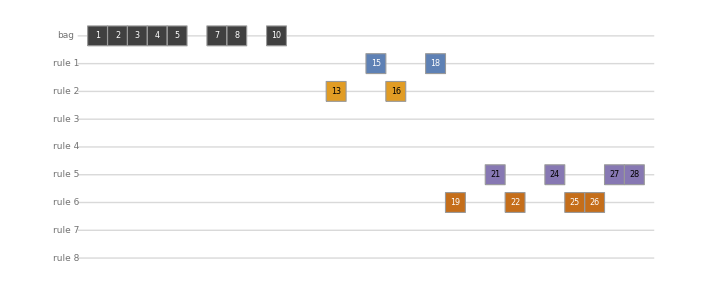
System5[-Graphics-]

```mathematica
CyclicTagSystemToSystem5[CyclicTagSystem[{{1}, {1, 0}}, {0, 1}], 1]
```

The sizes of every stage of the emulation of one step of a two-state machine by Wolfram's 2,3 machine:

```mathematica
EmulationSizes[{{1, 0} -> {0, 1, 1}}, {1, {}, 0, {}}, 1]
```

<|TagSymbols→169,TagWord→4,TagSteps→6,CyclicTagData→676,Appendants→338,System5Rules→8112,System5Integers→1476384,System5Steps→2177112,f→17513077,System4Elements→1136563671147,Wolfram23CellsAtLeast→1249664972135003846606848|>

### Properties and Relations

The All property is exactly the "Steps", "Value", and "Width" properties assembled into a triple:

```mathematica
OneSidedTuringMachineFunction[{600720, 3, 2}, 1, 32, All] === {OneSidedTuringMachineFunction[{600720, 3, 2}, 1, 32, "Steps"], OneSidedTuringMachineFunction[{600720, 3, 2}, 1, 32, "Value"], OneSidedTuringMachineFunction[{600720, 3, 2}, 1, 32, "Width"]}
```

True

The number of rows tabulated by the rule-space functions equals TuringMachineRuleCount:

```mathematica
TuringMachineRuleCount[2, 2] == Length[TuringMachineOutput[2, 2, 20, 2]]
```

True

### Possible Issues

A machine that does not halt within maxSteps reports Undefined for its value:

```mathematica
OneSidedTuringMachineFunction[{3, 2, 2}, 1, 50]
```

Undefined

With the All property the unresolved parts come back as Infinity:

```mathematica
OneSidedTuringMachineFunction[{3, 2, 2}, 1, 50, All]
```

{∞,Undefined,∞}

### Neat Examples

The space-time patterns of three different 2-state, 2-color machines on the same input 1, halting at values 3, 2, and 7:

```mathematica
GraphicsRow[OneSidedTuringMachinePlot[{#, 2, 2}, 1, 16, "LabelOutput" -> False] & /@ {1500, 1505, 1507}]
```

-Graphics-

## Source & Additional Information

### Creator

Wolfram Institute

### Source Control Repository

https://github.com/WolframInstitute/TuringMachine

### License

MIT License [»](https://resources.wolframcloud.com/PacletRepository/licenses/MIT)
 Apache License 2.0 [»](https://resources.wolframcloud.com/PacletRepository/licenses/Apache-2.0)
 Creative Commons Zero v1.0 Universal [»](https://resources.wolframcloud.com/PacletRepository/licenses/CC0-1.0)
 NoneA license is not required for personal deployments

### Keywords

Turing machine

one-sided Turing machine

multiway

nondeterministic

enumeration

NKS

universality

tag system

cyclic tag system

Wolfram 2

3 Turing machine

### Categories

Cloud & Deployment
 Data Manipulation & Analysis
 External Interfaces & Connections
 Geographic Data & Computation
 Graphs & Networks
 Images
 Machine Learning
 Scientific and Medical Data & Computation
 Sound & Video
 Symbolic & Numeric Computation
 Time-Related Computation
 Visualization & Graphics |  Core Language & Structure
 Engineering Data & Computation
 Financial Data & Computation
 Geometry
 Higher Mathematical Computation
 Knowledge Representation & Natural Language
 Notebook Documents & Presentation
 Social, Cultural & Linguistic Data
 Strings & Text
 System Operation & Setup
 User Interface Construction

### Related Resource Objects

TuringMachineFromNumber

TuringMachineToNumber

TuringMachineImport

Wolfram/Lambda

### Original Source References and Attributions

Stephen Wolfram, A New Kind of Science (Wolfram Media, 2002), Notes for Chapter 12, Section 8 (One-Sided Turing Machines), p. 1143

### Links

One-sided Turing machines — A New Kind of Science | Online (Note (d), p. 1143)

Wolfram (2,3) universality in Lean: the blueprint

### Compatibility

#### Wolfram Language Version

14.3+

#### Operating System

Windows |  Mac |  Linux

#### Environments

SessionLocal or cloud interactive session
 WebEvaluationCloud evaluation initiated by an HTTP request
 BatchJobRemote batch job |  ScriptScript run in batch mode
 WebAPIAPI called through an HTTP request
 |  SubkernelParallel or grid subkernel
 ScheduledScheduled task

#### Cloud Support

Supported in cloud

#### Required Features

Notebooks |  Parallel Kernels |  Cloud Access

### Disclosures

Local filesDisclosuresLocalFilesChoose this option if your paclet directly does any of the following during loading or normal usage:
◼ Creates, deletes or modifies local files
◼ Imports data from local files
File operations related to normal paclet installation and loading are excepted.Click for more information

Wolfram accountDisclosuresWolframAccountChoose this option if your paclet directly does any of the following:
◼ Requires, uses, or records any information related to user’s Wolfram ID
◼ Interacts with the user’s Cloud account or Wolfram account
◼ Creates, deletes or modifies the user’s cloud objects
◼ Creates or executes cloud deployed scheduled tasks
◼ Uses cloud credits, service credits or Wolfram credits
◼ Makes WolframAlpha callsClick for more information

External servicesDisclosuresExternalServicesChoose this option if your paclet directly does any of the following:
◼ Makes requests to external services (http, ftp, ssh, etc)
◼ Creates or uses service connection
◼ Send emailsClick for more information

Wolfram Language system configurationDisclosuresWLSystemConfigurationChoose this option if your paclet directly does any of the following:
◼ Creates persistent local scheduled tasks
◼ Modifies WL system or environment settings
◼ Modifies $Path, Directory, or similar
◼ Installs additional paclets or dependencies
◼ Creates or imports non-public ResourceObject content
◼ Makes FrontEnd modifications
◼ Internal handlersClick for more information

Wolfram Language built-in symbolsDisclosuresWLSystemSymbolsChoose this option if your paclet directly modifies definitions of built-in symbols such as those in System` or other internal contexts.Click for more information

Paclet dependenciesDisclosuresPacletDependenciesChoose this option if your paclet directly installs or updates any additional paclets. Paclets that are included with the Wolfram system do not require a disclosure.Click for more information

OS configurationDisclosuresOSConfigurationChoose this option if your paclet directly does any of the following:
◼ Modifies OS settings
◼ Makes any use of SystemCredentialClick for more information

Local system interactionsDisclosuresLocalSystemInteractionsChoose this option if your paclet directly does any of the following:
◼ Executes Shell or RUN commands
◼ Uses external evaluators via ExternalEvaluate
◼ Interacts with external libraries
◼ Reads or writes to streams or sockets
◼ Launches parallel kernels, subkernels or GPUsClick for more information

OtherDisclosuresOtherAdd additional text as needed in a new cell below to document any additional disclosures that are not listed above.Click for more information

## Author Notes

The paclet's Wolfram Language and Rust implementation and its worked examples are by Nik Murzin and Willem Nielsen. This Paclet Repository definition — its markdown source, metadata, and landing-page text — was drafted with help from Claude (Anthropic) and reviewed and edited by Nik Murzin. The one-sided Turing machine conventions follow Stephen Wolfram, A New Kind of Science, Note (d) for Section 12.8 (p. 1143). The functions for Smith's universality proof transcribe the Lean formalization in the repository's Proofs/ directory and are tested against it.